# Diffusion Limited Aggregation and Fractal Dimension

## Milan Cvitkovic

## Section 01: Introduction

In this notebook we will compare two methods for calculating the fractal dimension of a DLA cluster - a) by comparing the number of sites to the radius of gyration and b) by Gaylord and Wellin’s box counting method.  We will start by implementing code to generate a DLA cluster, implementing the code to do the calculations for methods a) and b), and then generate a DLA cluster to test our code.

## Section 02: Needed Packages

None.

## Section 03: Some Needed Statistical Functions

```mathematica
Clear[ave, aveSqr, var, unc]
ave[List_] := N[Apply[Plus,List]/Length[List]];
aveSqr[List_] := N[Apply[Plus,List^2]/Length[List]];
var[List_] := aveSqr[List]-ave[List]^2;
unc[List_] := Sqrt[var[List]/Length[List]]
```

Testing code:

```mathematica
Clear[TestList,a,b,c,d]
TestList = {a,b,c,d}
ave[TestList]
aveSqr[TestList]
var[TestList]
unc[TestList]
```

{a,b,c,d}

0.25 (a+b+c+d)

0.25 (a^2+b^2+c^2+d^2)

-0.0625 (a+b+c+d)^2+0.25 (a^2+b^2+c^2+d^2)

1/2 √(-0.0625 (a+b+c+d)^2+0.25 (a^2+b^2+c^2+d^2))

The symbolic interpretations are correct - all seem to work correctly.

## Section 04: Code to Generate and Visualize DLA Cluster

### Implementing Code

Creating the initial cluster site:

```mathematica
Clear[occupiuedSites]
occupiedSites={{0,0}}
```

{{0,0}}

Creating a formula for the walk-starting radius (s units wider than the max radius of the cluster):

```mathematica
Clear[rad,s]
s=10;
rad = Max[Abs[occupiedSites]]+s
```

10

Choosing a random location on the rad circle:

```mathematica
Round[rad {Cos[#],Sin[#]}]&[Random[Real,{0,N[2π]}]]
```

{7,-7}

Coding for each new step of the walk (applying random step to last output which is the last step that was made):

```mathematica
(#+{{1,0},{0,1},{-1,0},{0,-1}}[[Random[Integer,{1,4}]]])&;
```

Coding a check for when the random walking particle hits the cluster or the max allowed radius. The part before the or (the ||) is the check for if the distance of the random walking particle is outside the radius of the rad circle, the part after it checks whether :

```mathematica
(Apply[Plus,#^2]>(rad+s)^2||
Intersection[occupiedSites,Map[Function[y,y+#],{{1,0},{0,1},{-1,0},{0,-1}}]]≠{}&);
```

Putting the above pieces together to find the final location of the particle:

```mathematica
Clear[loc]
loc = FixedPoint[
(#+{{1,0},{0,1},{-1,0},{0,-1}}[[Random[Integer,{1,4}]]])&,
Round[rad {Cos[#],Sin[#]}]&[Random[Real,{0,N[2π]}]],
SameTest->(Apply[Plus,#2^2]>(rad+s)^2||
Intersection[occupiedSites,Map[Function[y,y+#2],{{1,0},{0,1},{-1,0},{0,-1}}]]≠{}&)
]
```

{-8,-19}

All the outputs generated by loc are either on the circle or next to the initial cluster, as we would expect

Now we check whether the output of loc was on the circle or next to the cluster, and add it if it was next to the cluster:

```mathematica
If[Apply[Plus,loc^2]≤(rad+s)^2,occupiedSites=Join[occupiedSites,{loc}]]
```

Repeating the new site generation and this test n times gives us our cluster:

```mathematica
While[Length[occupiedSites]<n,
rad = (Max[Abs[occupiedSites]]+s);
loc = FixedPoint[
(#+{{1,0},{0,1},{-1,0},{0,-1}}[[Random[Integer,{1,4}]]])&,
Round[rad {Cos[#],Sin[#]}]&[Random[Real,{0,N[2π]}]],
SameTest->(Apply[Plus,#2^2]>(rad+s)^2||
Intersection[occupiedSites,Map[Function[y,y+#2],{{1,0},{0,1},{-1,0},{0,-1}}]]≠{}&)];
If[Apply[Plus,loc^2]≤(rad+s)^2,occupiedSites=Join[occupiedSites,{loc}]]
]
```

Compiling all these parts into one Module:

```mathematica
Clear[DLA,n,s]
n=20;
s=10;
DLA[s_Integer,n_Integer]:=
Module[{loc,rad,particleCount=0,
stepChoices={{1,0},{0,1},{-1,0},{0,-1}}},
occupiedSites={{0,0}};
Monitor[While[Length[occupiedSites]<n,
++particleCount;
rad = Max[Abs[occupiedSites]]+s;
loc = FixedPoint[
(#+stepChoices[[Random[Integer,{1,4}]]])&,
Round[rad {Cos[#],Sin[#]}]&[Random[Real,{0,N[2π]}]],
SameTest->(Apply[Plus,#2^2]>(rad+s)^2||
Intersection[occupiedSites,Map[Function[y,y+#2],stepChoices]]≠{}&)];
If[Apply[Plus,loc^2]≤rad^2,occupiedSites=Join[occupiedSites,{loc}]]],particleCount]
;
Print["The number of particles released was ",particleCount];
occupiedSites]
```

### Implementing a Visalization to Check our Code

Implementing graphics code to display a DLA cluster, taking each site in the list, making it into a rectangle with a hue proportional to the time at which it was added, giving it a number, and then displaying it:

```mathematica
Clear[ShowDLA]
ShowDLA[sites_,opts___]:=
Module[{structure,s=Length[sites]},
structure={};
Map[(AppendTo[structure,
{Hue[0.99#/s],
Rectangle[sites[[#]]-{0.5,0.5},
sites[[#]]+{0.5,0.5}],
RGBColor[1,1,1],
Text[#,sites[[#]]]}])&,
Range[s]];
Show[Graphics[structure],
opts,
Axes-> None;
AspectRatio->Automatic,
PlotRange->All]
]
```

The number of particles released was 95

{{0,0},{-1,0},{1,0},{1,1},{1,-1},{1,2},{-1,1},{-2,1},{-3,1},{-4,1},{2,2},{-1,-1},{-5,1},{0,-1},{0,-2},{-5,2},{-5,0},{0,-3},{-6,1},{2,3}}

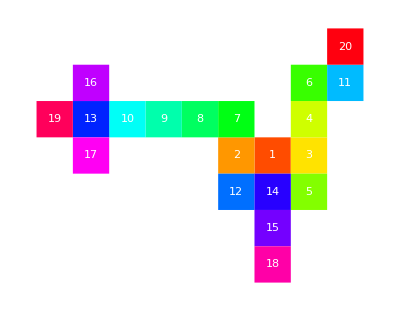

```mathematica
test01=DLA[10,20]
ShowDLA[test01]
```

We can also code this to display points rather than rectangles, which is faster:

```mathematica
Clear[ShowDLA2]
ShowDLA2[sites_,opts___Rule]:=
Module[{len=Length[sites],points,colors},
points=Map[Point,sites];
colors=Map[Hue,Range[len]/len];Show[Graphics[{PointSize[1/Sqrt[len]],Transpose[{colors,points}]},
opts,Axes->None,
AspectRatio->Automatic,
PlotRange->All]]]
```

The number of particles released was 74

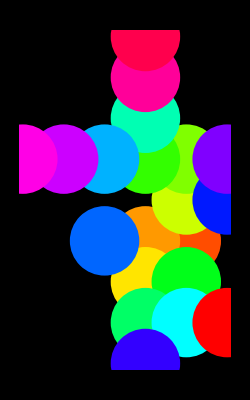

```mathematica
test02=DLA[10,20];
ShowDLA2[test02,Background->GrayLevel[0]]
```

These visualizations indicate that our DLA code is correctly creating DLA clusters

## Section 05: Method (a) - Code to Determine the Fractal Dimension Based on the Radius of Gyration

We will now develop code to find the fractal dimension of a DLA cluster using the radius of gyration.

From the class notes we know that the fractal dimension, d, is a variable in the equation n = c*r^d, where n is the number of sites in the cluster, c is a constant, and r is the radius of gyration.  If we monitor how n and r change for the growth of a particular cluster we can use regression techniques to find d, which will be the slope of a linear model fit of log[n] vs. log[r].

We will implement code to generate a list {r,n} for a single, already-formed cluster, then transform this into a list of {log[r],log[n]} and find the value of d from a linear fit.

### Module for Generating a List of {r,n} Values from the Guts of the Full Cluster List

To find the r, we’ll rely on our derivation from Assignment 08 that r^2 = (<x^2> - <x>^2) + (<y^2> - <y>^2) = Var(x)+Var(y).  Creating our module using our code for variance from Section 03:

```mathematica
findRG[inpCluster_]:=
Module[
{xyList,rgList,n},

rgList={};
(*separating the x and y values and finding the variance in each*)
xyList=Transpose[inpCluster];
(*finding the variance in x and y and taking the sqrt to get r, and putting this as the first value in a list {r,n}, repeating this for each n*)
Monitor[
For[n=1,n≤Length[inpCluster],n++,
AppendTo[rgList,
{Sqrt[var[Take[xyList[[1]],n]]+var[Take[xyList[[2]],n]]],n}
]
],n
];

rgList
];
```

Testing:

```mathematica
findRG[test01]
```

{{0.,1},{0.5,2},{0.816497,3},{0.935414,4},{1.0198,5},{1.21335,6},{1.26168,7},{1.41421,8},{1.64054,9},{1.9105,10},{2.02056,11},{1.99826,12},{2.2663,13},{2.23379,14},{2.25487,15},{2.44869,16},{2.5573,17},{2.62055,18},{2.77504,19},{2.86836,20}}

Qualitatively, based on the small test01 cluster, these r value seem reasonable for each n value (should start at 0, go to 0.5, and then start approaching some value).

### Module for Finding the Exponent d from a Log-Log Plot of {r,n} Values

Now we’ll create a module logRN[] which will take our rgList from above, find the best values for the slope and intercept of a log-log plot of r and n from nMin (must be greater than 2 and less than the full cluster size) to the full cluster, and output a list {intercept (log[c]), slope (d)} and a list {error in log[c], error in d}:

```mathematica
logRN[rgList_,nMin_]:=
Module[
{logList,bestLogFits,z},

logList=LinearModelFit[N[Log[Drop[rgList,nMin-1]]],z,z];

Print["{Log[c],d} are: "];
Print[bestLogFits = logList["BestFitParameters"]];
Print["errors in Log[c] and d are: "];
Print[bestLogFits = logList["ParameterErrors"]];
]
```

Testing:

```mathematica
logRN[findRG[test01],2]
```

{Log[c],d} are:

{1.53615,1.35909}

errors in Log[c] and d are:

{0.025063,0.0361826}

The output is in the correct form, and the d value for our test list is 1.34±0.04, which if nothing else is at least between 1 and 2 which is what we would expect for the fractal dimesion of a 2D DLA cluster.

## Section 06: Method (b) - Code to Determine the Fractal Dimension Based on the Box Counting Method

We will now develop code to find the fractal dimension of a DLA cluster using Gaylord and Wellin’s box counting method.

First we will create a list of ordered pairs {diameter,site density for that diameter}:

```mathematica
fractalDataList=Table[{2r,occSiteDensity[r]},{r,Max[Abs[occupiedSites]]}];
```

Writing the code to get site density for a particular diameter:

```mathematica
occSiteDensity[t_Integer]:=N[Count[occupiedSites,{x_?(Abs[#]≤t&),y_?(Abs[#]≤t&)}]]/(2t+1)^2
occSiteDensity[4]
```

0.234568

Writing the function to get the fractal dimension (the occupiedSites list is coming from the notebook for Problem25):

```mathematica
Clear[x]
fractalDim = Fit[N[Log[fractalDataList]],{1,x},x]
```

0.374908-0.868569 x

Putting all the code together into a module (remembering that we have to add 2 to the output from this code to get fractal dimension):

```mathematica
Clear[r]
FractalDimension[occupiedSites_List]:=
Module[{occSiteDensity,fractalDataList,fractaldim},occSiteDensity[t_Integer]:=N[Count[occupiedSites,{x_?(Abs[#]≤t&),y_?(Abs[#]≤t&)}]]/(2t+1)^2;

fractalDataList=Table[{2r,occSiteDensity[r]},{r,Max[Abs[occupiedSites]]}];
fractalDim = LinearModelFit[N[Log[fractalDataList]],{1,z},z];

Print["{log[c], d} for our DLA is: "];
Print[fractalDim["BestFitParameters"]+2];
Print["our errors in Log[c] and d are: "];
Print[fractalDim["ParameterErrors"]];
]
```

Testing:

```mathematica
FractalDimension[test01]
```

{log[c], d} for our DLA is:

{2.74814,0.870218}

our errors in Log[c] and d are:

{0.107638,0.0569769}

Thus we find that the fractal dimension in our test cluster test01 is d=0.87±0.06, which is quite different from the fractal dimension calculated by method (a).

## Section 07: Putting it All Together - Calculating the Fractal Dimension of a Large DLA Cluster using Methods (a) and (b)

Now that we have working code for both our methods to calculate the fractal dimension of a DLA cluster, we will generate a large cluster, calculate the fractal dimension by both methods, and compare them:

Generating a DLA cluster of 1000 with a particle starting radius of 10 spaces wider than the cluster’s max radius:

```mathematica
DLA01=DLA[10,2000];
```

The number of particles released was 8942

(Note: This probably seems like a very small cluster size, but it took about an hour to run on a lab computer which wasn’t doing anything else.  My code doesn’t seem to be very efficient...)

Now finding the fracal dimension with method (a) using cluster sizes from 500 to 1000:

```mathematica
logRN[findRG[DLA01],1000]
```

{Log[c],d} are:

{0.699283,1.82119}

errors in Log[c] and d are:

{0.00496349,0.00137009}

And method (b):

```mathematica
FractalDimension[DLA01]
```

{log[c], d} for our DLA is:

{2.47376,1.45867}

our errors in Log[c] and d are:

{0.0817892,0.0192489}

## Section 08: Conclusions

We found the fractal dimension of a 2000 particle DLA cluster (with particle starting radius of 10+max radius of cluster) to be 1.821±0.001 by method (a) (using cluster sizes from 1000 to 2000) and 1.46±0.02 by method (b).  Likely due to the relatively small cluster size of 2000, the values calculated by both methods are not within standard error of each other.  Method (a) gave a value with smaller error, and it also used only large cluster sizes, so it is likely a better estimate of fractal dimension in this case.  Both values, however, are relatively near each other and both are reasonable answers (given that they are between 1 and 2).